# Allan Vriance - like Plot of DNA Seqence

## 準備

```mathematica
Get["/home/kamano/SCRIPT-MATHEMATICA/SCRIPTS/DNA_sequence_operations.txt"]
```

```mathematica
Timing[Do[EuclideanDistance[{1,1,0,1},{0,0,1,1}];,{100000}]]
```

{0.802878,Null}

```mathematica
Timing[Do[Tr[({1,1,0,1}-{0,0,1,1})^2];,{100000}]]
```

{0.861869,Null}

## Allan Variance Plot 手順

ベクトル a = {a1,a2,a3...}とする。

時間幅(window の大きさ)wを決定する

ベクトルa より、幅wからなるすべてのサブリストを生成する

すべての隣接するサブリスト(window) 間の平均差をとる

その平均差の値を2 乗したものの平均に、1/2 を掛けた値がAllan Variance と
なる

上記1-4 のステップを、可能なwにつき行う

wを横軸座標に、対応するAllan Variance のルートを縦軸座標に、両対数プロッ
トしたものがAllan Variance Plot である

アランバリアンスの式 :

```mathematica
allanVar[ylist_,w_]:=1/2 Mean[(ListCorrelate[Append[PadRight[{-1},w],1],MovingAverage[ylist,w]])^2]
```

```mathematica
Append[PadRight[{-1},3],1]
```

{-1,0,0,1}

```mathematica
l1={1,1,2,3,4,5,5}
```

{1,1,2,3,4,5,5}

```mathematica
PadRight[{-1},3]
```

{-1,0,0}

```mathematica
MovingAverage[l1,3]
```

{4/3,2,3,4,14/3}

```mathematica
ListCorrelate[{-1,1},MovingAverage[l1,3]]
```

{2/3,1,1,2/3}

```mathematica
{2-4/3,3-2,4-3,14/3-4}
```

{2/3,1,1,2/3}

```mathematica
ListCorrelate[{-1,0,1},MovingAverage[l1,3]]
```

{5/3,2,5/3}

```mathematica
{3-4/3,4-2,14/3-3}
```

{5/3,2,5/3}

```mathematica
MovingAverage[l1,3]
```

{4/3,2,3,4,14/3}

```mathematica
2-4/3
```

2/3

```mathematica
Union[ Table[Round[10^((i-1)Log[10,1000]/2000)],{i,1,2000+1}]]/.{i->4}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,316,317,318,319,320,321,322,323,324,325,327,328,329,330,331,332,333,335,336,337,338,339,340,342,343,344,345,346,348,349,350,351,352,354,355,356,357,359,360,361,362,363,365,366,367,369,370,371,372,374,375,376,378,379,380,382,383,384,385,387,388,389,391,392,394,395,396,398,399,400,402,403,405,406,407,409,410,412,413,414,416,417,419,420,422,423,425,426,428,429,431,432,434,435,437,438,440,441,443,444,446,447,449,450,452,453,455,457,458,460,461,463,465,466,468,469,471,473,474,476,478,479,481,483,484,486,488,489,491,493,494,496,498,499,501,503,505,506,508,510,512,513,515,517,519,521,522,524,526,528,530,531,533,535,537,539,541,543,545,546,548,550,552,554,556,558,560,562,564,566,568,570,571,573,575,577,579,581,583,585,587,590,592,594,596,598,600,602,604,606,608,610,612,614,617,619,621,623,625,627,630,632,634,636,638,640,643,645,647,649,652,654,656,658,661,663,665,668,670,672,675,677,679,682,684,686,689,691,693,696,698,701,703,706,708,710,713,715,718,720,723,725,728,730,733,735,738,740,743,746,748,751,753,756,759,761,764,766,769,772,774,777,780,783,785,788,791,793,796,799,802,804,807,810,813,816,818,821,824,827,830,833,836,838,841,844,847,850,853,856,859,862,865,868,871,874,877,880,883,886,889,892,895,898,902,905,908,911,914,917,920,924,927,930,933,936,940,943,946,950,953,956,959,963,966,969,973,976,979,983,986,990,993,997,1000}

```mathematica
Length[%]
```

648

```mathematica
Log[10,1000]
```

3

```mathematica
Union[ Table[i,{i,1,1024+1}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025}

```mathematica
Union[ Table[i,{i,1,Npts+1}]]/.{Npts->1024}
```

Table::iterb: Iterator {i, 1, 1 + Npts} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025}

```mathematica
Sin[2Pi]
```

0

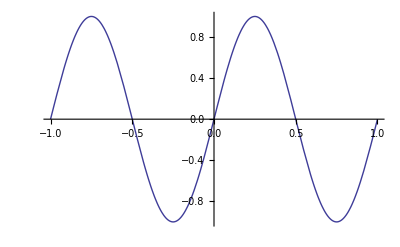

```mathematica
Plot[Sin[2Pi i],{i,-1,1}]
```

### Plot example (from Wolfram MathSource)

```mathematica
Manipulate[
Module[{Ntot,opts,ylist,g1,g2,Npts,τdata,σdata,στdata},
Ntot=5000;
opts=Sequence[Frame->True,Axes->False,Joined->True,GridLines->Automatic,BaseStyle->12,ImageSize->480];
ylist=RandomReal[NormalDistribution[0,a],Ntot]+b Cos[(2 π)/T Range[Ntot]]+d Range[Ntot];
g1=ListPlot[ylist,FrameLabel->{"t [s]","y(t)"},PlotRange->{All,{-0.4,0.4}},AspectRatio->0.17,opts];
Npts=30;
τdata=Union[ Table[Round[10^((i-1)Log[10,1000]/Npts)],{i,1,Npts+1}]];
σdata=√allanVar[ylist,#]& /@ τdata;
στdata=Transpose[{τdata,σdata}];
g2=Show[
ListLogLogPlot[στdata,PlotMarkers->Automatic,FrameLabel->{"τ [s]","σ_y(τ)"},PlotRange->{All,{0.00009,0.2}},AspectRatio->0.48,opts,FrameTicks->{{1,10,100,1000},{{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"}},None,None}],
LogLogPlot[b Sin[π τ /T]^2/ (π τ/T),{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,RGBColor[.49,0,0]}]],
LogLogPlot[d τ/√2,{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,Darker@RGBColor[.6,.73,.36]}]]
];
Column[{g1,g2}]
],
{{a,0.05,"white frequency noise amplitude"},0.01,0.1,Appearance->"Labeled"},
{{b,0.012,"oscillation amplitude"},0,0.1,Appearance->"Labeled"},
{{T,100,"oscillation period (s)"},10,1000,Appearance->"Labeled"},
{{d,0.000005,"drift (1/s)"},0,0.0001,Appearance->"Labeled"},
SaveDefinitions->True,TrackedSymbols:>{a,b,T,d}
]
```

## Allan Variance Plot DNA塩基配列への応用手順

DNA 塩基配列データを、a = {a1,a2,a3...}とする(a1、a2... は、塩基)。

部分塩基配列(window) の大きさw 決定する

全塩基配列データa より、幅w からなるすべての部分塩基配列を生成する

すべての隣接する部分塩基配列(window) 間の距離をとる

距離はオリゴヌクレオチド頻度ベクトルにおけるユークリッド距離とする

オリゴヌクレオチド頻度は部分配列において取りうるすべてのオリゴヌク
レオチド長n を考える

その距離を2 乗したものの平均に、1/2 を掛けた値がAllan Variance 様値となる

上記1-4 のステップを、可能なw、n につき行う

各nにつき、w を横軸座標に、対応するAllan Variance 様値のルートを縦軸座
標に、両対数プロットしたものがAllan Variance 様Plot となる

アランバリアンス様値の式 :

DNAシークエンスを用意

```mathematica
dnaseq="AAGTTTCGGGGCATTTTGCCCCA"
```

AAGTTTCGGGGCATTTTGCCCCA

1. 部分塩基配列 (window) の大きさw 決定する (w=7)

2. 全塩基配列データa より、幅w からなるすべての部分塩基配列を生成する

```mathematica
dnasubseqs=seqToSubseqs[dnaseq,7]
```

{AAGTTTC,AGTTTCG,GTTTCGG,TTTCGGG,TTCGGGG,TCGGGGC,CGGGGCA,GGGGCAT,GGGCATT,GGCATTT,GCATTTT,CATTTTG,ATTTTGC,TTTTGCC,TTTGCCC,TTGCCCC,TGCCCCA}

3.1. すべての隣接配列のペアを生成

```mathematica
contactPair[dnasubseqs,7]
```

{{AAGTTTC,GGGGCAT},{AGTTTCG,GGGCATT},{GTTTCGG,GGCATTT},{TTTCGGG,GCATTTT},{TTCGGGG,CATTTTG},{TCGGGGC,ATTTTGC},{CGGGGCA,TTTTGCC},{GGGGCAT,TTTGCCC},{GGGCATT,TTGCCCC},{GGCATTT,TGCCCCA}}

1 - 3. wを決定(w=7) - すべての部分配列を生成(seqToSubseqs) - nを決定(n=3) - 部分配列をベクトルに変換(oligonucToVec) - すべての隣接ベクトルのペアを生成(contactPair)

```mathematica
(cpvec[7,3]=contactPair[Map[oligonucToVec[#,3]&,seqToSubseqs[dnaseq,7]],7])//Dimensions
```

{10,2,64}

4. その距離を2 乗したものの平均に、1/2 を掛けた値がAllan Variance 様値となる

```mathematica
AllanDNA[7,3]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,cpvec[7,3]//N]]/2
```

5.8

1 - 4. を一気に行う

```mathematica
AllanDNA[7,1]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,1]&,seqToSubseqs[dnaseq,7]],7]//N]]/2
```

6.5

```mathematica
AllanDNA[7,2]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,2]&,seqToSubseqs[dnaseq,7]],7]//N]]/2
```

8.1

```mathematica
AllanDNA[7,3]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,3]&,seqToSubseqs[dnaseq,7]],7]//N]]/2
```

5.8

## Allan Variance Plot DNA塩基配列への応用例

### PolyA

```mathematica
testSeqPolyA=StringJoin[Table["A",{500}]];
```

```mathematica
AbsoluteTiming[AllanDNA["A",100,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[testSeqPolyA,w]],w]//N]]/2,{w,10,100,10},{n,1,5}]]]
```

{12.56859,{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}}

### PolyACGT

```mathematica
testSeqPolyACGT=StringJoin[Table["ACGT",{500}]];
```

```mathematica
testSeqPolyagct=StringJoin[Table["agct",{500}]];
```

長さ500*4のシークエンス
w: 4から16
n: 1から4

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

{7.363607,{{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.}}}

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[testSeqPolyagct,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

{7.418341,{{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,4]//TableForm
```

0. | 0. | 0. | 0.
1. | 0. | 1. | 1.
2. | 1. | 0. | 1.
1. | 1. | 1. | 0.
0. | 0. | 0. | 0.
1. | 0. | 1. | 1.
2. | 1. | 0. | 1.
1. | 1. | 1. | 0.
0. | 0. | 0. | 0.
1. | 0. | 1. | 1.
2. | 1. | 0. | 1.
1. | 1. | 1. | 0.
0. | 0. | 0. | 0.

```mathematica
ListPlot3D[AllanDNA["ACGT",4,16,1,4]]
```

-Graphics3D-

```mathematica
AbsoluteTiming[AllanDNA["ACGT",5,16,5,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,5,16},{n,5,5}]]]
```

{17.69559,{{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.}}}

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,1]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,1}]]]
```

{0.484889,{{0.},{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,1]
```

{{0.},{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.}}

## Mathematica Script作成

dir:
/home/kamano/TEST_COLLECTION/AllanVarianceLike-Plot/bin/

アウトプット:
*.out.list

条件:
(window size;oligonucleotide length): 4-128;1-4(que[1]), 129-256;1-4(que[2]), 257-384;1-4(que[3]), 385-512;1-4(que[4]).

## ファージ X174シークエンスの結果の Get[]とプロット

```mathematica
quedir="/home/kamano/TEST_COLLECTION/AllanVarianceLike-Plot/bin/"
```

/home/kamano/TEST_COLLECTION/AllanVarianceLike-Plot/bin/

```mathematica
(que[1]=Get[quedir<>"allanDNA_x174.4.128.1.4.out.list"])//Dimensions
(que[1]=Join[{{0,0,0,0},{0,0,0,0},{0,0,0,0}},que[1]])//Dimensions
```

{125,4}

{128,4}

```mathematica
(que[2]=Get[quedir<>"allanDNA_x174.129.256.1.4.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[3]=Get[quedir<>"allanDNA_x174.257.384.1.4.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[4]=Get[quedir<>"allanDNA_x174.385.512.1.4.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[8]=Get[quedir<>"allanDNA_x174.8.128.5.8.out.list"])//Dimensions
(que[8]=Join[Table[0,{7},{4}],que[8]])//Dimensions
```

{121,4}

{128,4}

```mathematica
(que[5]=Get[quedir<>"allanDNA_x174.129.256.5.8.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[6]=Get[quedir<>"allanDNA_x174.257.384.5.8.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[7]=Get[quedir<>"allanDNA_x174.385.512.5.8.out.list"])//Dimensions
```

{128,4}

```mathematica
(que["1-4"]=Join[que[1],que[2],que[3],que[4]])//Dimensions
```

{512,4}

```mathematica
(que["5-8"]=Join[que[8],que[5],que[6],que[7]])//Dimensions
```

{512,4}

```mathematica
(que["All"]=Transpose[Join[Transpose[que["1-4"]],Transpose[que["5-8"]]]])//Dimensions
```

{512,8}

```mathematica
ListPlot3D[que["All"]]
```

-Graphics3D-

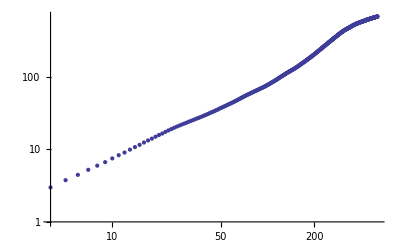
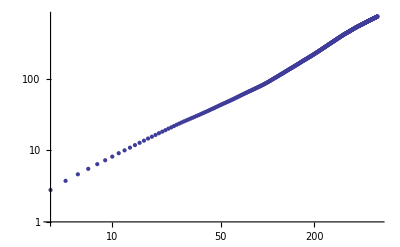
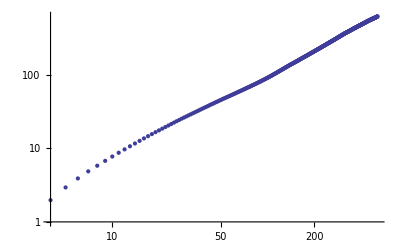
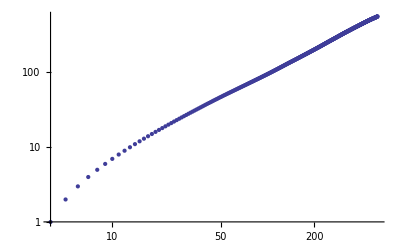
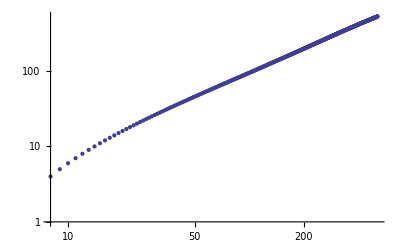
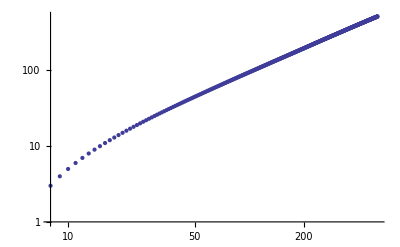
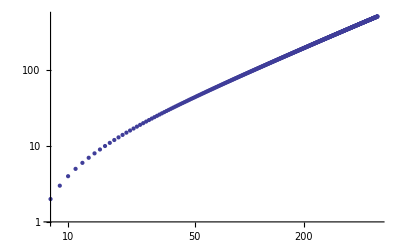
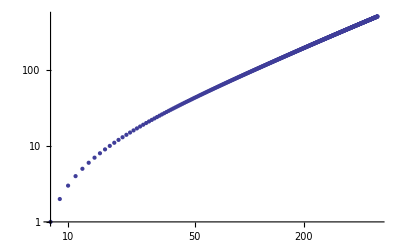

```mathematica
Table[
ListLogLogPlot[Transpose[que["All"]][[n]]],{n,1,8}
]
```

## C. elegansシークエンス

```mathematica
CEfile="/BANK/SEQUENCE/genome/ncbi/genomes/Caenorhabditis_elegans/CHR_III/NC_003281.fasta"
```

/BANK/SEQUENCE/genome/ncbi/genomes/Caenorhabditis_elegans/CHR_III/NC_003281.fasta

```mathematica
(CEseq=Import[CEfile][[1]])//StringLength
```

13783700

```mathematica
AbsoluteTiming[AllanDNA["CEseq",4,64,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[CEseq,w]],w]//N]]/2,{w,4,64},{n,1,4}]]]
```

## 計算メモ

```mathematica
oligonucToVec["GGANTTt",3]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Position[Out[32],1]
```

{}

```mathematica
combinatorialSeqJoin[3]//Flatten
```

{AAA,AAC,AAG,AAT,ACA,ACC,ACG,ACT,AGA,AGC,AGG,AGT,ATA,ATC,ATG,ATT,CAA,CAC,CAG,CAT,CCA,CCC,CCG,CCT,CGA,CGC,CGG,CGT,CTA,CTC,CTG,CTT,GAA,GAC,GAG,GAT,GCA,GCC,GCG,GCT,GGA,GGC,GGG,GGT,GTA,GTC,GTG,GTT,TAA,TAC,TAG,TAT,TCA,TCC,TCG,TCT,TGA,TGC,TGG,TGT,TTA,TTC,TTG,TTT}

```mathematica
Position[Out[34],"GGA"]
```

{}

## Export

```mathematica
Export["/BANK/SEQUENCE/test/AGCT.fasta",testSeqPolyACGT]
```

Export::nodir: Directory "/BANK/SEQUENCE/test/" does not exist.

Export::noopen: Cannot open "/BANK/SEQUENCE/test/AGCT.fasta".

$Failed